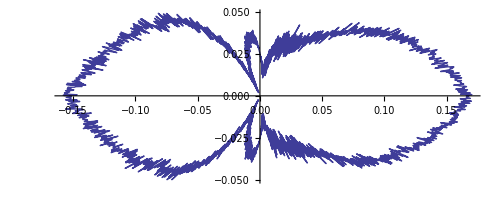

```mathematica
MyPlot = With[{lambda=1},With[{r= 25,k=2 Pi/lambda,eta=120 Pi,I0=1,l=lambda/50},PolarPlot[2.5*10^16Abs[Sum[((2n+1)/(n(n+1)))(AmnCoefs[[n]][[n+m+1]]Mfunc[m,n,k,r,thetaValue,0] + BmnCoefs[[n]][[n+m+1]]Nfunc[m,n,k,r,thetaValue,0]),{n,1,numberOfModes},{m,-n,n}]],{thetaValue,-Pi,Pi}]]]
```

```mathematica
Show[%48,ImageSize->Large]
```

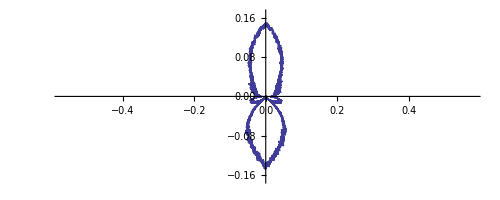

```mathematica
Rotate[MyPlot,Pi/2]
```

-Graphics-

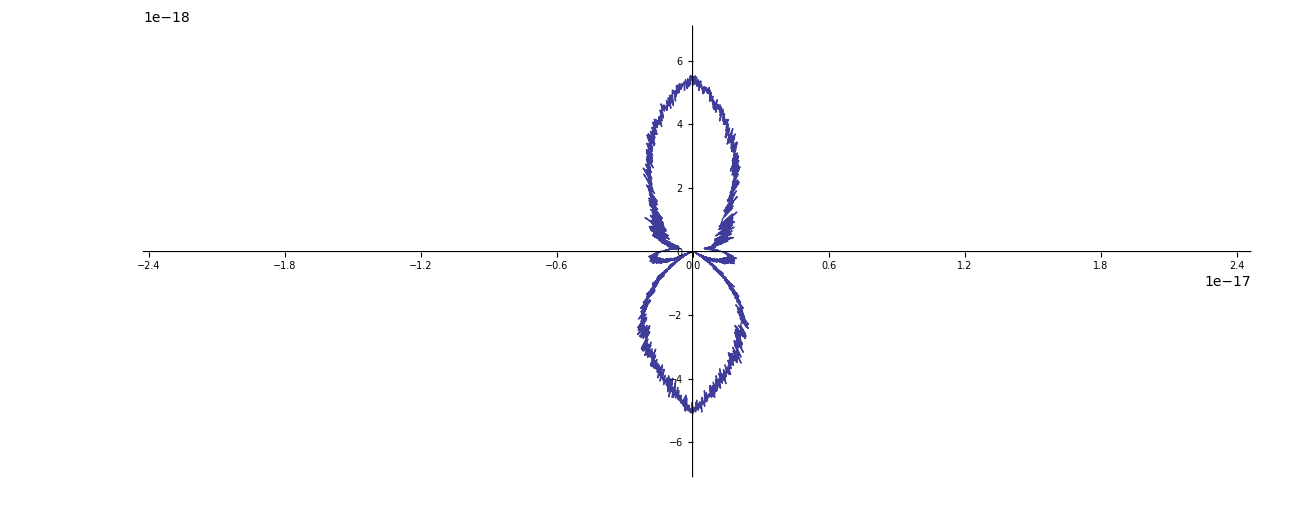

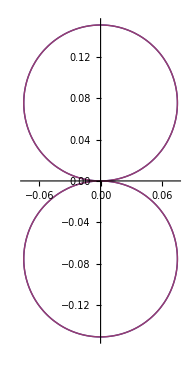

```mathematica
With[{lambda=1},With[{r= 25,k=2 Pi/lambda,eta=120 Pi,I0=1,l=lambda/50},PolarPlot[{Abs[Edipoletheta[r,thetaValue,k,eta,l,I0]],Abs[Sum[((2n+1)/(n(n+1)))(AmnCoefs[[n]][[n+m+1]]Mfunc[m,n,k,r,thetaValue,0] + BmnCoefs[[n]][[n+m+1]]Nfunc[m,n,k,r,thetaValue,0]),{n,1,numberOfModes},{m,-n,n}]]},{thetaValue,-Pi,Pi}]]]
```

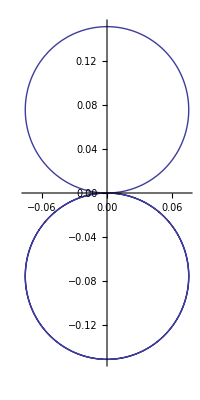

```mathematica
With[{lambda=1},With[{r= 25,k=2 Pi/lambda,eta=120 Pi,I0=1,l=lambda/50},PolarPlot[Abs[Sum[((2n+1)/(n(n+1)))(AmnCoefs[[n]][[n+m+1]]Mfunc[m,n,k,r,thetaValue,0] + BmnCoefs[[n]][[n+m+1]]Nfunc[m,n,k,r,thetaValue,0]),{n,1,numberOfModes},{m,-n,n}]],{thetaValue,-Pi,2Pi}]]]
```

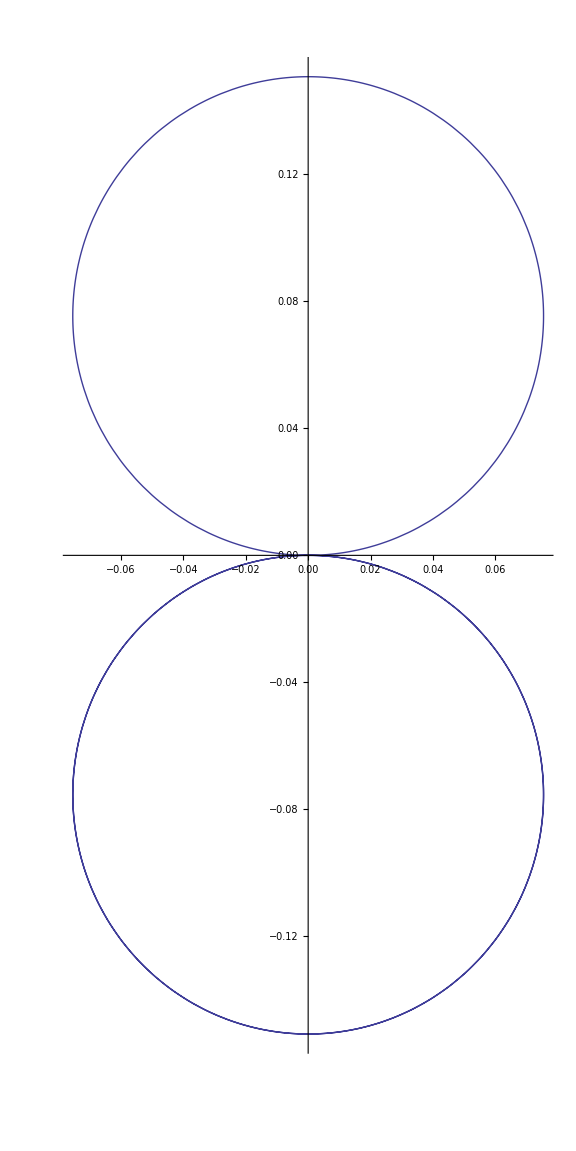

```mathematica
Show[%52,ImageSize->Large]
```

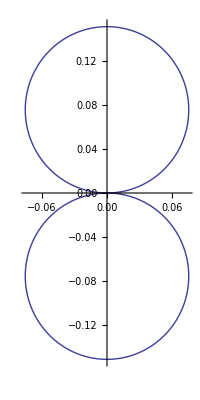

```mathematica
With[{lambda=1},With[{r= 25,k=2 Pi/lambda,eta=120 Pi,I0=1,l=lambda/50},PolarPlot[Abs[Edipoletheta[r,thetaValue,k,eta,l,I0]],{thetaValue,-Pi,Pi}]]]
```

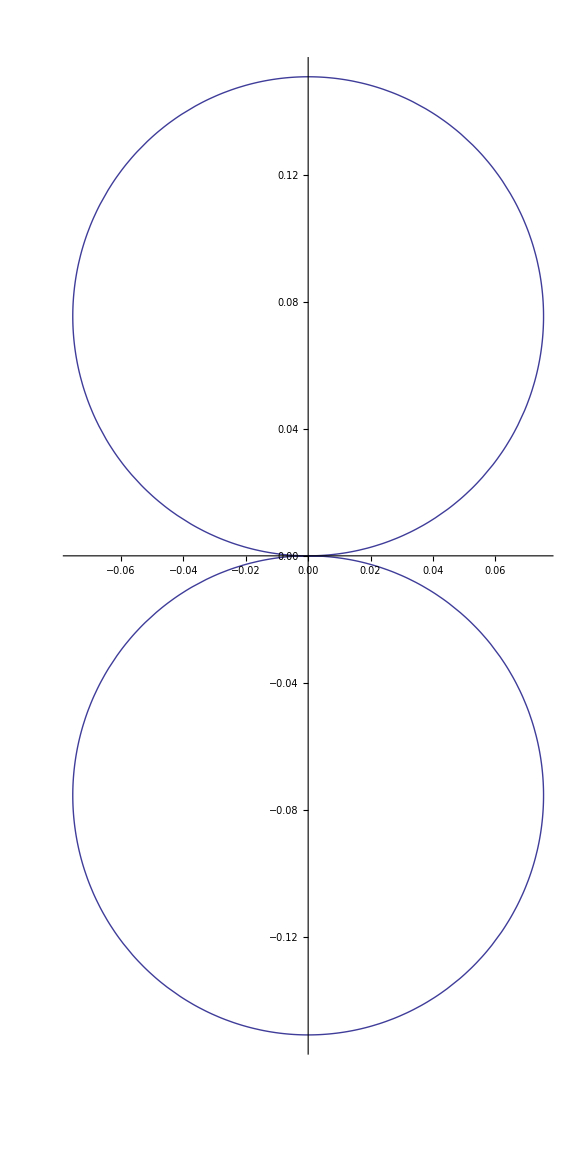

```mathematica
Show[%53,ImageSize->Large]
```